```mathematica
enV=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"];
enVs1=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_enVs1.dat"];
enVs2=Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_enVs2.dat"];
```

```mathematica
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefV[r].mx
<<C:\\Users\\ASUS\\Documents\\TestDATA_δefVs2[r].mx
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-10;a=1;αSch=2.;V[r_]=-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636r))/r;VCou[r_]=-α/r;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2[r_]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086}//Simplify;
```

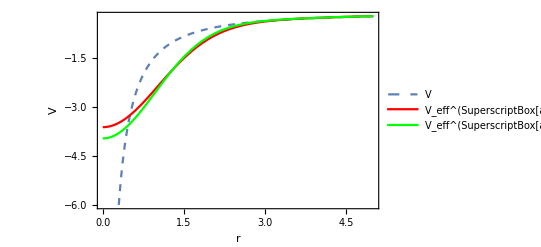

```mathematica
Plot[{V[r],Vs1[r],Vs2[r]},{r,0,5},PlotStyle->{Dashed,Red,Green},ImageSize->Full,PlotLegends->{"V","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},Frame->True,PlotRange->{{0,5},{0,-6}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"r"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\NoFourierTransformation.eps",%];
```

```mathematica
Limit[Integrate[Rationalize[(1.0415223038416566 ⅇ^(-0.9990999998788636r))/r] E^(I k r Cos[θ])E^(-I ϵ r)r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π},Assumptions->Re[(0.-1. ⅈ) ϵ]<0.9990999998788636&&Re[(0.+1. ⅈ) ϵ]≥-0.9990999998788637+1. Abs[Im[k]]],ϵ->0]
```

13.0882/(0.998201+k^2)

```mathematica
-(4 π)/k^2-13.088155273195458/(0.9982008097579451+k^2)//Expand
```

-13.0882/(0.998201+k^2)-(4 π)/k^2

```mathematica
Integrate[Rationalize[V[r]] E^(I k r Cos[θ])E^(-I ϵ r)r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

ConditionalExpression[-13.0882/(0.998201+1. k^2+((0.+1.9982 ⅈ)-1. ϵ) ϵ)-12.5664/(1. k^2-1. ϵ^2),Re[(0.-1. ⅈ) ϵ]<0&&Re[(0.+1. ⅈ) ϵ]≥Abs[Im[k]]]

```mathematica
Limit[-13.088155273195458/(0.9982008097579451+1. k^2+((0.+1.998199999757727 ⅈ)-1. ϵ) ϵ)-12.566370614359172/(1. k^2-1. ϵ^2),ϵ->0]
```

(-12.5438-25.6545 k^2)/(k^2 (0.998201+1. k^2))

```mathematica
Vs2[r][[1]]
```

ⅇ^(-r^2/2) (-3.15845+0.20734 r^2)

```mathematica
Integrate[Rationalize[Vs1[r][[2]]] E^(I k r Cos[θ])E^(-I ϵ r)r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

ConditionalExpression[-(2 ⅇ^(-1/2 (k+ϵ)^2) π (ⅇ^(2 k ϵ) (k+ϵ) (1+ⅈ Erfi[(k-ϵ)/(√2)])+(k-ϵ) (1-ⅈ Erfi[(k+ϵ)/(√2)])))/(k (k-ϵ) (k+ϵ)),Abs[Im[k]]+Im[ϵ]<0]

```mathematica
Integrate[Rationalize[Vs1[r][[1]]] E^(I k r Cos[θ])E^(-I ϵ r)r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

-(22.1472 ⅇ^(-1/2 (k+ϵ)^2) (ⅇ^(2 k ϵ) (k-ϵ) (1+ⅈ Erfi[(k-ϵ)/(√2)])+(k+ϵ) (1-ⅈ Erfi[(k+ϵ)/(√2)])))/k

```mathematica
Limit[-(2 ⅇ^(-1/2 (k+ϵ)^2) π (ⅇ^(2 k ϵ) (k+ϵ) (1+ⅈ Erfi[(k-ϵ)/(√2)])+(k-ϵ) (1-ⅈ Erfi[(k+ϵ)/(√2)])))/(k (k-ϵ) (k+ϵ)),ϵ->0]+Limit[-1/k 22.147190698243392 ⅇ^(-1/2 (k+ϵ)^2) (ⅇ^(2 k ϵ) (k-ϵ) (1+ⅈ Erfi[(k-ϵ)/(√2)])+(k+ϵ) (1-ⅈ Erfi[(k+ϵ)/(√2)])),ϵ->0]
```

-44.2944 ⅇ^(-k^2/2)-(4 ⅇ^(-k^2/2) π)/k^2

```mathematica
Integrate[Rationalize[Vs2[r][[2]]] E^(I k r Cos[θ])E^(-I ϵ r)r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

ConditionalExpression[-(2 ⅇ^(-1/2 (k+ϵ)^2) π (ⅇ^(2 k ϵ) (k+ϵ) (1+ⅈ Erfi[(k-ϵ)/(√2)])+(k-ϵ) (1-ⅈ Erfi[(k+ϵ)/(√2)])))/(k (k-ϵ) (k+ϵ)),Abs[Im[k]]+Im[ϵ]<0]

```mathematica
Integrate[Rationalize[Vs2[r][[1]]] E^(I k r Cos[θ])E^(-I ϵ r)r^2 Sin[θ],{r,0,∞},{θ,0,π},{ϕ,0,2π}]
```

1/k ⅇ^(-1/2 (k+ϵ)^2) (-19.9739 k-19.9739 ⅇ^(2 k ϵ) k-1.63276 k^3-1.63276 ⅇ^(2 k ϵ) k^3-19.9739 ϵ+19.9739 ⅇ^(2 k ϵ) ϵ-(0.+5.21101 ⅈ) ⅇ^(1/2 (k+ϵ)^2) k ϵ-4.89828 k^2 ϵ+4.89828 ⅇ^(2 k ϵ) k^2 ϵ-4.89828 k ϵ^2-4.89828 ⅇ^(2 k ϵ) k ϵ^2-1.63276 ϵ^3+1.63276 ⅇ^(2 k ϵ) ϵ^3+ⅇ^(2 k ϵ) ((0.-1.63276 ⅈ) k^3+(0.+19.9739 ⅈ) ϵ+(0.+4.89828 ⅈ) k^2 ϵ+(0.+1.63276 ⅈ) ϵ^3+k ((0.-19.9739 ⅈ)-(0.+4.89828 ⅈ) ϵ^2)) Erfi[(k-ϵ)/(√2)]+((0.+19.9739 ⅈ) k+(0.+1.63276 ⅈ) k^3+(0.+19.9739 ⅈ) ϵ+(0.+4.89828 ⅈ) k^2 ϵ+(0.+4.89828 ⅈ) k ϵ^2+(0.+1.63276 ⅈ) ϵ^3) Erfi[(k+ϵ)/(√2)])

```mathematica
Limit[-(2 ⅇ^(-1/2 (k+ϵ)^2) π (ⅇ^(2 k ϵ) (k+ϵ) (1+ⅈ Erfi[(k-ϵ)/(√2)])+(k-ϵ) (1-ⅈ Erfi[(k+ϵ)/(√2)])))/(k (k-ϵ) (k+ϵ)),ϵ->0]+Limit[1/k ⅇ^(-1/2 (k+ϵ)^2) (-19.973861414113536 k-19.973861414113536 ⅇ^(2 k ϵ) k-1.6327592230850427 k^3-1.6327592230850427 ⅇ^(2 k ϵ) k^3-19.973861414113536 ϵ+19.973861414113536 ⅇ^(2 k ϵ) ϵ-(0.+5.211013502432148 ⅈ) ⅇ^(1/2 (k+ϵ)^2) k ϵ-4.898277669255129 k^2 ϵ+4.898277669255129 ⅇ^(2 k ϵ) k^2 ϵ-4.898277669255129 k ϵ^2-4.898277669255129 ⅇ^(2 k ϵ) k ϵ^2-1.6327592230850427 ϵ^3+1.6327592230850427 ⅇ^(2 k ϵ) ϵ^3+ⅇ^(2 k ϵ) ((0.-1.6327592230850427 ⅈ) k^3+(0.+19.973861414113536 ⅈ) ϵ+(0.+4.898277669255129 ⅈ) k^2 ϵ+(0.+1.6327592230850427 ⅈ) ϵ^3+k ((0.-19.973861414113536 ⅈ)-(0.+4.898277669255129 ⅈ) ϵ^2)) Erfi[(k-ϵ)/(√2)]+((0.+19.973861414113536 ⅈ) k+(0.+1.6327592230850427 ⅈ) k^3+(0.+19.973861414113536 ⅈ) ϵ+(0.+4.898277669255129 ⅈ) k^2 ϵ+(0.+4.898277669255129 ⅈ) k ϵ^2+(0.+1.6327592230850427 ⅈ) ϵ^3) Erfi[(k+ϵ)/(√2)]),ϵ->0]
```

ⅇ^(-0.5 k^2) (-39.9477-3.26552 k^2)-(4 ⅇ^(-k^2/2) π)/k^2

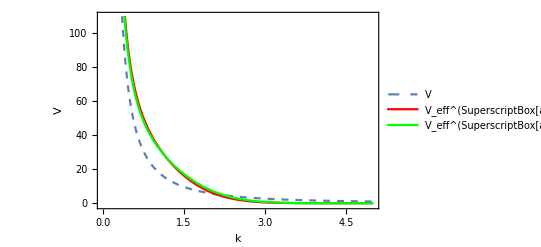

```mathematica
Plot[{Abs@%86,Abs@%87,Abs@%88},{k,0,5},ImageSize->Full,PlotStyle->{Dashed,Red,Green},PlotLegends->{"V","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},Frame->True,PlotRange->{{0,5},{-1,110}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"k"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\FourierTransformation_1.eps",%];
```

```mathematica
{%8,%9,%10}//Expand
```

{-25.6545/(0.998201+k^2)-12.5438/(k^2 (0.998201+k^2)),-44.2944 ⅇ^(-0.5 k^2)-(12.5664 ⅇ^(-0.5 k^2))/k^2,-39.9477 ⅇ^(-0.5 k^2)-(12.5664 ⅇ^(-0.5 k^2))/k^2-3.26552 ⅇ^(-0.5 k^2) k^2}

```mathematica
{V[r],Vs1[r],Vs2[r]}
```

{-1/r-(1.04152 ⅇ^(-0.9991 r))/r,-2.81241 ⅇ^(-r^2/2)-Erf[r/(√2)]/r,-2.53643 ⅇ^(-r^2/2)+3.26552 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r}

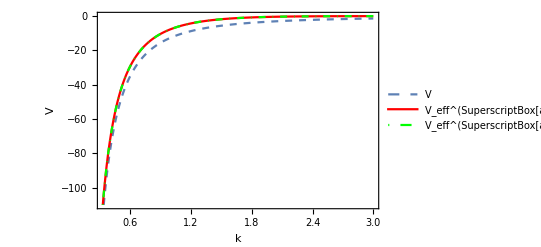

```mathematica
Plot[{-(4 π)/k^2,-(4 ⅇ^(-k^2/2) π)/k^2,-(4 ⅇ^(-k^2/2) π)/k^2},{k,0,3},ImageSize->Full,PlotStyle->{Dashed,{Red},{DotDashed,Green}},PlotLegends->{"V","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},Frame->True,PlotRange->{{0,3},{0,-110}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"k"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\FourierTransformation_2.eps",%];
```

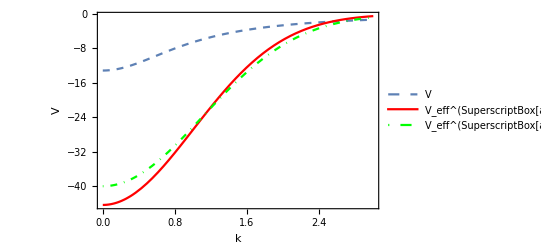

```mathematica
Plot[{-13.088155273195458/(0.9982008097579451+k^2),-44.294381396486784 ⅇ^(-k^2/2),ⅇ^(-0.5 k^2) (-39.94772282822707-3.2655184461700855 k^2)},{k,0,3},ImageSize->Full,PlotStyle->{Dashed,Red,{DotDashed,Green}},PlotLegends->{"V","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},Frame->True,PlotRange->{{0,3},{0.0,-50}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"k"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\FourierTransformation_3.eps",%];
```

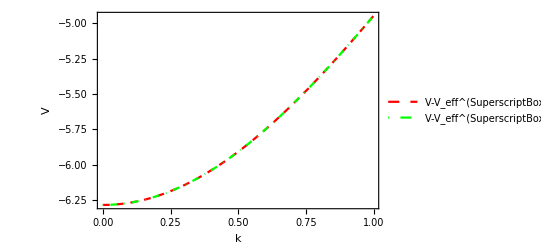

```mathematica
Plot[{-(4 π)/k^2+(4 ⅇ^(-k^2/2) π)/k^2,-(4 π)/k^2+(4 ⅇ^(-k^2/2) π)/k^2},{k,0.0001,1},ImageSize->Full,PlotStyle->{{Dashed,Red},{DotDashed,Green}},PlotLegends->{"V-V_eff^(SuperscriptBox[a, 2])","V-V_eff^(SuperscriptBox[a, 4])"},Frame->True,PlotRange->Reverse@{{-4.95,-6.5},{0,1}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"k"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\FourierTransformation_4.eps",%];
```

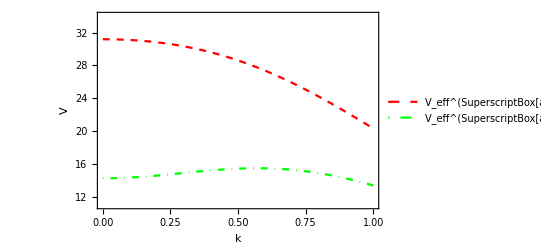

```mathematica
Plot[{-13.088155273195458/(0.9982008097579451+k^2)+44.294381396486784 ⅇ^(-k^2/2),-25.65452588755463/(0.9982008097579451+k^2)-ⅇ^(-0.5 k^2) (-39.94772282822707-3.2655184461700855 k^2)},{k,0,1},ImageSize->Full,PlotStyle->{{Dashed,Red},{DotDashed,Green}},PlotLegends->{"V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},Frame->True,PlotRange->{{0,1},{11,34}},Axes->False,FrameLabel->{{"V",None},Reverse@{None,"k"}},RotateLabel->False,FrameTicks->{{All,None},Reverse@{None,All}}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\FourierTransformation_5.eps",%];
```